```mathematica
Rad=ReadList["d:/lattice/data/mat.dat",{Number,Number, Number}];
RadEff=ReadList["d:/lattice/data/mateff.dat",{Number,Number, Number}];
Diff={};
Do[Diff=Append[Diff,
{Rad[[i]][[1]],Rad[[i]][[2]],Rad[[i]][[3]]-RadEff[[i]][[3]]/((Rad[[i]][[3]]-RadEff[[i]][[3]])/2)}]
,{i,Length[Rad]}];
Export["d:/lattice/data/diffmat.dat", Diff]
```

d:/lattice/data/diffmat.dat

```mathematica
arad[t_]:=Sqrt[1+t/16];
alam[t_]:=Exp[1+t/16]/Exp[1];
```

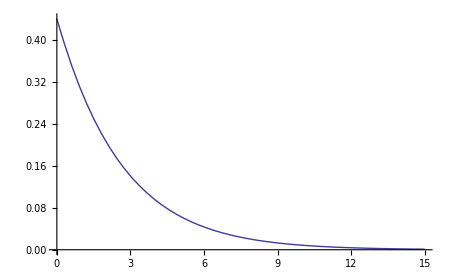

```mathematica
a[t_]:=alam[t];
b[t_]:=0.88/(a[t]^5+a[t]^7);
Plot[b[t],{t,0,15}]
```

```mathematica
a[t_]:=alam[t];
beff[b_,t_]:=b*(a[t]^5+a[t]^7)/2;
Plot3D[beff[b,t],{b,4,0.5},{t,12,15}]
```

-Graphics3D-

```mathematica
beff[0.1,1]
```

95.0678

```mathematica
N[Exp[2]^7]
```

1.2026×10^6